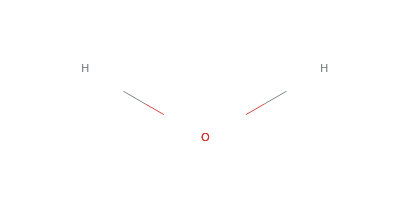

```mathematica
ChemicalData["Water"]
```

```mathematica
coords=ChemicalData["Water","AtomPositions"]/.q_Quantity:>QuantityMagnitude[q]
```

{{-6.3259,-25.268,26.21},{74.277,26.059,17.009},{-67.951,-0.79118,-43.219}}

```mathematica
types=ChemicalData["Water","VertexTypes"]
```

{O,H,H}

```mathematica
bonds=ChemicalData["Water","EdgeRules"]
```

{1→2,1→3}

```mathematica
ElementData["Hydrogen","IconColor"]
```

RGBColor[0.93, 1, 1]

```mathematica
moleculePlot[{atoms:{__String},bonds:{__Rule},coords:{{_Real,_Real,_Real}..}}]:=
Module[{spheres,cylinders={}},
spheres=MapThread[{ElementData[Switch[#1,"O","Oxygen","H","Hydrogen","C","Carbon"],"IconColor"],Sphere[#2,Switch[#1,"H",24,_,31]]}&,{atoms,coords}];
cylinders=Apply[{LightGray,Cylinder[{coords⟦#1⟧,coords⟦#2⟧},10]}&,List@@@bonds,{1}];
Graphics3D[{spheres,cylinders},BoxRatios->Automatic,Boxed->False]
]
```

```mathematica
moleculePlot[{types,bonds,coords}]
```

-Graphics3D-

```mathematica
coordsMD=Map[RandomReal[{-20,20}]+#&,Table[coords,{100}],{3}];
First@%
```

{{2.8722,-37.3329,28.3125},{85.7262,9.84981,22.1979},{-70.9035,17.3013,-47.635}}

```mathematica
First@coords
```

{-6.3259,-25.268,26.21}

```mathematica
ListAnimate[moleculePlot[{types,bonds,#}]&/@coordsMD]
```